# A variational framework for near-optimal Bayesian quantum estimation of Gaussian states

This notebook contains symbolic calculations for estimation of a displacement parameter encoded in the x mean of a Gaussian state. 

Last updated: 18/08/26.

## Linear basis {1,Δx} with Gaussian prior (exact)

Basis B_i is {1,Δx} where Δx=x̂-⟨x⟩_ρ_0

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];(*Gaussian prior *)

(*First moments of rho0*)
avgx0=Integrate[(x0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
avgp=p0 ;

(*Second moments of rho0*)
avgx2ρ0=Integrate[(Vxx+(x0+θ)^2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;
avgp2ρ0=Vpp+p0^2;


(*Gram matrix *)
Gmat=({{1, 0, 0}, {0, avgx2ρ0-avgx0^2, 0}, {0, 0, avgp2ρ0-avgp^2}});
Gmat//MatrixForm
```

(1 | 0 | 0
0 | Vxx+σ0^2 | 0
0 | 0 | Vpp)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  
bx=Integrate[θ (x0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-avgx0*μ0//Simplify  
bp=0

bvec={b0,bx,bp};
bvec//Simplify
```

μ0

σ0^2

0

{μ0,σ0^2,0}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* To second order in prior width Subscript[σ, 0] *)
αSeries=Normal[Series[αopt,{σ0,0,2}]]//Simplify
```

{μ0,σ0^2/(Vxx+σ0^2),0}

{μ0,σ0^2/Vxx,0}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

λ-bvec.Inverse[Gmat].bvec//Simplify
```

μ0^2+σ0^2

(Vxx σ0^2)/(Vxx+σ0^2)

## Linear basis {1,Δx,Δp} with Gaussian prior and displacement in x and p

Basis B_i is {1,Δx,Δp} where Δx=x̂-⟨x⟩_ρ_0

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];(*Gaussian prior *)

(*First moments of rho0*)
avgx0=Integrate[(x0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
avgp0=Integrate[(p0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;

avgxp0=Vxp+Integrate[(x0+θ)*(p0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] -avgx0*avgp0;

(*Second moments of rho0*)
avgx2ρ0=Integrate[(Vxx+(x0+θ)^2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;
avgp2ρ0=Integrate[(Vpp+(p0+θ)^2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;


(*Gram matrix *)
Gmat=({{1, 0, 0}, {0, avgx2ρ0-avgx0^2, avgxp0}, {0, avgxp0, avgp2ρ0-avgp0^2}});
Gmat//MatrixForm
```

(1 | 0 | 0
0 | Vxx+σ0^2 | Vxp+σ0^2
0 | Vxp+σ0^2 | Vpp+σ0^2)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  
bx=Integrate[θ (x0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-avgx0*μ0//Simplify  
bp=Integrate[θ (p0+θ) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-avgp0*μ0//Simplify 

bvec={b0,bx,bp};
bvec//Simplify
```

μ0

σ0^2

σ0^2

{μ0,σ0^2,σ0^2}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* To second order in prior width Subscript[σ, 0] *)
αSeries=Normal[Series[αopt,{σ0,0,2}]]//Simplify
```

{μ0,((Vpp-Vxp) σ0^2)/(-Vxp^2-2 Vxp σ0^2+Vxx σ0^2+Vpp (Vxx+σ0^2)),((-Vxp+Vxx) σ0^2)/(-Vxp^2-2 Vxp σ0^2+Vxx σ0^2+Vpp (Vxx+σ0^2))}

{μ0,((Vpp-Vxp) σ0^2)/(-Vxp^2+Vpp Vxx),((Vxp-Vxx) σ0^2)/(Vxp^2-Vpp Vxx)}

```mathematica
(*The optimal homodyne angle is then tan(ϕ)= *)
αopt[[3]]/αopt[[2]]//Simplify
```

(-Vxp+Vxx)/(Vpp-Vxp)

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL=λ-bvec.Inverse[Gmat].bvec//FullSimplify
```

μ0^2+σ0^2

((Vxp^2-Vpp Vxx) σ0^2)/(Vxp^2-Vpp Vxx-(Vpp-2 Vxp+Vxx) σ0^2)

```mathematica
MSL/.{Vxp->0}//FullSimplify
MSL/.{Vxp->0,Vpp->Vxx}//FullSimplify
```

(Vpp Vxx σ0^2)/(Vpp Vxx+(Vpp+Vxx) σ0^2)

(Vxx σ0^2)/(Vxx+2 σ0^2)

```mathematica
Series[MSL,{σ0,0,4}]//Simplify
```

σ0^2+((Vpp-2 Vxp+Vxx) σ0^4)/(Vxp^2-Vpp Vxx)+O[σ0]^5

Now see MSL for arbitrary squeezed probe state

```mathematica
MSL/.{Vxx->Cosh[2r]-Cos[ϕ]*Sinh[2r],Vpp->Cosh[2r]+Cos[ϕ]*Sinh[2r],Vxp->Sin[ϕ]*Sinh[2r]}//FullSimplify
```

σ0^2/(1+2 σ0^2 (Cosh[2 r]-Sin[ϕ] Sinh[2 r]))

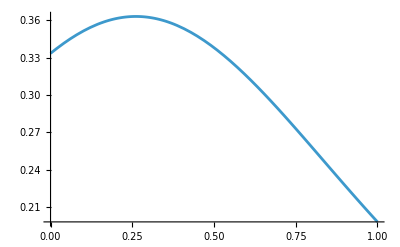

```mathematica
Plot[σ0^2/(1+2 σ0^2 (Cosh[2 r]-Sin[ϕ] Sinh[2 r]))/.{σ0->1,ϕ->0.5},{r,0,1}]
```

```mathematica
Solve[D[(Cosh[2 r]-Sin[ϕ] Sinh[2 r]),r]==0,r]
```

{{r→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[-(√(-1-Sin[ϕ]))/(√(-1+Sin[ϕ]))]), C[1]∈ℤ]},{r→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[(√(-1-Sin[ϕ]))/(√(-1+Sin[ϕ]))]), C[1]∈ℤ]}}

```mathematica
1/2 Log[(√(-1-Sin[ϕ]))/(√(-1+Sin[ϕ]))]/.ϕ->0.5
```

0.261119+0. ⅈ

```mathematica
1/4 Log[-1-2/(-1+Sin[ϕ])]/.ϕ->0.5
```

0.261119

## Theorem 1: Calculating W_(ρ̄)/W_ρ_0

```mathematica
cov={{Vxx,0},{0,Vpp}};

Wρ=PDF[MultinormalDistribution[{x0+θ,p0},cov],{x,p}]; (* Wigner function of state *)

p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ]; (* Gaussian prior *)
```

```mathematica
Wρ0=Integrate[Wρ*p[θ],{θ,-Infinity,Infinity},Assumptions->{σ0,Vxx,Vpp} ∈ PositiveReals]

Wρbar=Integrate[θ*Wρ*p[θ],{θ,-Infinity,Infinity},Assumptions->{σ0,Vxx,Vpp} ∈ PositiveReals]
```

(ⅇ^(1/2 (-p^2/Vpp+(2 p p0)/Vpp-p0^2/Vpp-(-x+x0+μ0)^2/(Vxx+σ0^2))))/(2 π √(Vpp (Vxx+σ0^2)))

(ⅇ^(1/2 (-p^2/Vpp+(2 p p0)/Vpp-p0^2/Vpp-(-x+x0+μ0)^2/(Vxx+σ0^2))) (Vxx μ0+(x-x0) σ0^2))/(2 π √(Vpp+(Vpp Vxx)/σ0^2) σ0 (Vxx+σ0^2))

```mathematica
Simplify[Wρbar/Wρ0,Assumptions->{σ0,Vxx,Vpp} ∈ PositiveReals]
```

(Vxx μ0+(x-x0) σ0^2)/(Vxx+σ0^2)

```mathematica
cov//MatrixForm
```

(Vxx | 0
0 | Vpp)

```mathematica
Det[({{Vxx+σ0^2, 0}, {0, Vpp}})]
```

Vpp Vxx+Vpp σ0^2

```mathematica
Simplify[Abs[Eigenvalues[ⅈ ({{0, 1}, {-1, 0}}).({{Vxx+σ0^2, 0}, {0, Vpp}})]],Assumptions->{σ0,Vxx,Vpp} ∈ PositiveReals] (* Symplectic eigenvalues *)
```

{√(Vpp (Vxx+σ0^2)),√(Vpp (Vxx+σ0^2))}

## Showing that the posterior mean is the same linear shrinkage estimator

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];(*Gaussian prior *)

likelihood[θ_,x_,x0_]:=PDF[NormalDistribution[x0+θ,Vxx],x];(*Gaussian likelihood of x-homodyne measurements. This comes the p-marginal of the (Gaussian) Wigner function *)
```

```mathematica
evidence=Integrate[likelihood[θ,x,x0]*p[θ],{θ,-Infinity,Infinity},Assumptions->{σ0,Vxx} ∈ PositiveReals]
```

(ⅇ^(-(-x+x0+μ0)^2/(2 (Vxx^2+σ0^2))))/(√(2 π) √(Vxx^2+σ0^2))

```mathematica
Integrate[evidence,{x,-Infinity,Infinity},Assumptions->{σ0,Vxx} ∈ PositiveReals] (*The normalisation of the posterior, i.e. the evidence, is already normalised*)
```

1

```mathematica
posterior[θ_,x_,x0_]:=(likelihood[θ,x,x0]*p[θ])/evidence (*The posterior from Bayes rule*)
```

The posterior mean is then

```mathematica
Integrate[θ*posterior[θ,x,x0],{θ,-Infinity,Infinity},Assumptions->{σ0,Vxx} ∈ PositiveReals]
```

(Vxx^2 μ0+(x-x0) σ0^2)/(Vxx^2+σ0^2)

```mathematica
(* Symmetry of prior around its mean *)
p[μ0-θ]==p[μ0+θ]//Simplify
p[2μ0-θ]==p[θ]//Simplify

(* Symmetry of likelihood around its mean for fixed θ *)
likelihood[θ,x0+θ+x,x0]==likelihood[θ,x0+θ-x,x0]//Simplify
likelihood[θ,2(x0+θ)-x,x0]==likelihood[θ,x,x0]//Simplify

(* Symmetry of likelihood around its mean for fixed x *)
likelihood[x-x0+θ,x,x0]==likelihood[ (x-x0)-θ,x,x0]//Simplify
likelihood[2(x-x0)-θ,x,x0]==likelihood[θ,x,x0]//Simplify
```

True

True

True

«3 more identical outputs»

## Linear basis {1,Δx} with uniform prior

Basis B_i is {1,Δx} where Δx=x̂-⟨x⟩_ρ_0

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=1/Δ; (*Uniform prior *)

(*First moments of rho0*)
avgx0=Integrate[(x0+θ) p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;

(*Gram matrix element*)
Gxx=Integrate[(Expand[(x-avgx0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify;


(*Gram matrix *)
Gmat=({{1, 0}, {0, Gxx}})//Simplify;
Gmat//MatrixForm
```

(1 | 0
0 | Vxx+Δ^2/12)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;
bx=Integrate[θ (x-avgx0)p[θ]/.x->(x0+θ),{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] //Simplify  

bvec={b0,bx}//Simplify;
bvec
```

Δ^2/12

{μ0,Δ^2/12}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* Write in terms of prior variance *)
αopt /. Δ^2->12*σ0^2//Simplify
```

{μ0,Δ^2/(12 Vxx+Δ^2)}

{μ0,σ0^2/(Vxx+σ0^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->σ0>0]//Simplify

λ-bvec.Inverse[Gmat].bvec//Simplify
```

Δ^2/12+μ0^2

(Vxx Δ^2)/(12 Vxx+Δ^2)

```mathematica
(* Check MSL is invariant under linear change of basis *)

U={{a,b},{c,d}};

λ-(U.bvec).Inverse[U.Gmat.Transpose[U]].(U.bvec)//Simplify
```

(Vxx Δ^2)/(12 Vxx+Δ^2)

## Linear basis {1, Δx_ϕ} with uniform prior

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=1/Δ; (*Uniform prior *)

avgxϕ0=Integrate[((x0+θ)*Cos[ϕ]+p0*Sin[ϕ] )p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;

Gxϕxϕ=Integrate[(Expand[(x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ),q^2->p0^2+Vpp,q->p0},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify;

(*Gram matrix *)
Gmat=({{1, 0}, {0, Gxϕxϕ}})//Simplify;
Gmat//MatrixForm
```

(1 | 0
0 | (Vxx+Δ^2/12) Cos[ϕ]^2+Vpp Sin[ϕ]^2)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;
bxϕ=Integrate[θ (x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0 ) p[θ]/.{x->(x0+θ),q->p0},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] //Simplify  

bvec={b0,bxϕ}//Simplify;
bvec
```

1/12 Δ^2 Cos[ϕ]

{μ0,1/12 Δ^2 Cos[ϕ]}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]
```

{μ0,(Δ^2 Cos[ϕ])/((12 Vxx+Δ^2) Cos[ϕ]^2+12 Vpp Sin[ϕ]^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->σ0>0]//Simplify

MSL=λ-bvec.Inverse[Gmat].bvec//Simplify

(* Write in terms of prior variance *)
MSL /. Δ^2->12*σ0^2//Simplify
```

Δ^2/12+μ0^2

(Δ^2 (Vxx Cos[ϕ]^2+Vpp Sin[ϕ]^2))/((12 Vxx+Δ^2) Cos[ϕ]^2+12 Vpp Sin[ϕ]^2)

(σ0^2 (Vxx Cos[ϕ]^2+Vpp Sin[ϕ]^2))/((Vxx+σ0^2) Cos[ϕ]^2+Vpp Sin[ϕ]^2)

```mathematica
MSL/.ϕ->0
MSL/.ϕ->π/2
```

(Vxx Δ^2)/(12 Vxx+Δ^2)

Δ^2/12

## Basis {1,Δx,Δx^2} with uniform prior (shows no improvement)

Basis B_i is {1,Δx,Δx^2} where Δx=x̂-⟨x⟩_ρ_0.

It turns out that this has the same MSL as the basis {1,Δx}, which implies that Δx^2 is not included in the posterior mean.

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=1/Δ; (*Uniform prior *)
avgx0=Integrate[(x0+θ) p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;

Gxx=Integrate[(Expand[(x-avgx0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

Gx2x2=Integrate[(Expand[(x-avgx0)^4]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify


(*Gram matrix *)
Gmat=({{1, 0, Gxx}, {0, Gxx, 0}, {Gxx, 0, Gx2x2}});
Gmat//MatrixForm
```

Vxx+Δ^2/12

3 Vxx^2+(Vxx Δ^2)/2+Δ^4/80

(1 | 0 | Vxx+Δ^2/12
0 | Vxx+Δ^2/12 | 0
Vxx+Δ^2/12 | 0 | 3 Vxx^2+(Vxx Δ^2)/2+Δ^4/80)

```mathematica
(* Check that odd moments like Subscript[⟨Δx^3⟩, Subscript[ρ, 0]]=Subscript[⟨(x-Subscript[⟨x⟩, Subscript[ρ, 0]])^3⟩, Subscript[ρ, 0]]=0*)
Integrate[(Expand[(x-avgx0)^3]) p[θ]/.{x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify
Integrate[((x0+θ)^3+3*(x0+θ)*Vxx-3*avgx0*((x0+θ)^2+Vxx)+3*(x0+θ)*avgx0^2 -avgx0^3) p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify
```

0

0

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;
bx=Integrate[θ((x-avgx0)) p[θ]/.{x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify
bx2=Integrate[θ(Expand[(x-avgx0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

bvec={b0,bx,bx2};
bvec//Simplify
```

Δ^2/12

Vxx μ0+(Δ^2 μ0)/12

{μ0,Δ^2/12,Vxx μ0+(Δ^2 μ0)/12}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* Write in terms of prior variance *)
αopt /. Δ^2->12*σ0^2//Simplify
```

{μ0,Δ^2/(12 Vxx+Δ^2),0}

{μ0,σ0^2/(Vxx+σ0^2),0}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->σ0>0]//Simplify

MSL=λ-bvec.Inverse[Gmat].bvec//Simplify
```

Δ^2/12+μ0^2

(Vxx Δ^2)/(12 Vxx+Δ^2)

```mathematica
(* Using row reduction (Subscript[G, x^2]-Subscript[G, x])Subscript[α, x^2]=Subscript[b, x^2]-Subscript[μ, 0] Subscript[G, x]*)

bx2-μ0*Gxx//Simplify

(* Since the RHS=0 then Subscript[α, x^2]=0*)
```

0

### Now use Gram-Schmidt to get orthogonal basis first

```mathematica
B1=1;
B2=x-avgx0;

B3=Collect[(x-avgx0)^2-Simplify[Integrate[(Expand[(x-avgx0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]],x,Simplify]
```

-Vxx+x^2+x0^2-Δ^2/12+2 x0 μ0+μ0^2-2 x (x0+μ0)

```mathematica
B3==(x-avgx0)^2-(Vxx+Δ^2/12)//Simplify
```

True

This means that the basis which makes G_ij=⟨B_i,B_j⟩_ρ_0 diagonal is {1, Δx, Δx^2-(V_xx+σ_0^2)} where Δx^2=(x̂-⟨x⟩_ρ_0)^2.

```mathematica
Simplify[Integrate[(Expand[{B1*B2,B1*B3,B2*B3}]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]]

G22=Integrate[(Expand[B2*B2]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

G33=Integrate[(Expand[B3*B3]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify


(*Gram matrix *)
Gmat=({{1, 0, 0}, {0, G22, 0}, {0, 0, G33}});
Gmat//MatrixForm
```

{0,0,0}

Vxx+Δ^2/12

2 Vxx^2+(Vxx Δ^2)/3+Δ^4/180

(1 | 0 | 0
0 | Vxx+Δ^2/12 | 0
0 | 0 | 2 Vxx^2+(Vxx Δ^2)/3+Δ^4/180)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;
bx=Integrate[θ*B2 p[θ]/.{x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0];//Simplify
bx2=Integrate[θ*B3 p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0];//Simplify

bvec={b0,bx,bx2};
bvec//Simplify
```

{μ0,Δ^2/12,0}

```mathematica
Expand[B3] /.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)}//Simplify
```

-Δ^2/12+(θ-μ0)^2

```mathematica
(* Check that the x^4 term does not contribute too *)

B4=Collect[(x-avgx0)^4-Simplify[Integrate[(Expand[(x-avgx0)^4]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]],x,Simplify]

bx4=Integrate[θ*B4 p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify
```

-3 Vxx^2+x^4+x0^4-(Vxx Δ^2)/2-Δ^4/80+4 x0^3 μ0+6 x0^2 μ0^2+4 x0 μ0^3+μ0^4-4 x^3 (x0+μ0)+6 x^2 (x0+μ0)^2-4 x (x0+μ0)^3

0

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* Write in terms of prior variance *)
αopt /. Δ^2->12*σ0^2//Simplify
```

{μ0,Δ^2/(12 Vxx+Δ^2),0}

{μ0,σ0^2/(Vxx+σ0^2),0}

## Basis {1,Δx,Δx^3} with uniform prior (shows improvement)

Basis B_i is {1,Δx,Δx^3} where Δx=x̂-⟨x⟩_ρ_0.

It turns out that this has the same MSL as the basis {1,Δx}, which implies that Δx^2 is not included in the posterior mean.i d

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=1/Δ; (*Uniform prior *)
avgx0=Integrate[(x0+θ) p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;

Gx3=Integrate[(Expand[(x-avgx0)^3]) p[θ]/.{x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

Gxx=Integrate[(Expand[(x-avgx0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

Gxx3=Integrate[(Expand[(x-avgx0)^4]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

Gx3x3=Integrate[(Expand[(x-avgx0)^6]) p[θ]/.{x^6->(x0+θ)^6+15*(x0+θ)^4*Vxx+45*(x0+θ)^2*Vxx^2+15*Vxx^3,x^5->(x0+θ)^5+10*(x0+θ)^3*Vxx+15*(x0+θ)*Vxx^2,x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify


(*Gram matrix *)
Gmat=({{1, 0, Gx3}, {0, Gxx, Gxx3}, {Gx3, Gxx3, Gx3x3}});
Gmat//MatrixForm
```

0

Vxx+Δ^2/12

3 Vxx^2+(Vxx Δ^2)/2+Δ^4/80

1/448 (6720 Vxx^3+1680 Vxx^2 Δ^2+84 Vxx Δ^4+Δ^6)

(1 | 0 | 0
0 | Vxx+Δ^2/12 | 3 Vxx^2+(Vxx Δ^2)/2+Δ^4/80
0 | 3 Vxx^2+(Vxx Δ^2)/2+Δ^4/80 | 1/448 (6720 Vxx^3+1680 Vxx^2 Δ^2+84 Vxx Δ^4+Δ^6))

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;
bx=Integrate[θ((x-avgx0)) p[θ]/.{x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify
bx3=Integrate[θ(Expand[(x-avgx0)^3]) p[θ]/.{x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

bvec={b0,bx,bx3};
bvec//Simplify
```

Δ^2/12

1/80 (20 Vxx Δ^2+Δ^4)

{μ0,Δ^2/12,1/80 (20 Vxx Δ^2+Δ^4)}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* Write in terms of prior variance *)
αopt /. Δ^2->12*σ0^2//Simplify
```

{μ0,(16800 Vxx^3 Δ^2+5040 Vxx^2 Δ^4+210 Vxx Δ^6+Δ^8)/(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8),-(280 Vxx Δ^4)/(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)}

{μ0,(5040 Vxx^2 Δ^4+210 Vxx Δ^6+Δ^8+201600 Vxx^3 σ0^2)/(201600 Vxx^4+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8+806400 Vxx^3 σ0^2),-(280 Vxx Δ^4)/(201600 Vxx^4+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8+806400 Vxx^3 σ0^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->σ0>0]//Simplify

MSL=λ-bvec.Inverse[Gmat].bvec//Simplify
```

Δ^2/12+μ0^2

(Vxx Δ^2 (16800 Vxx^3+4200 Vxx^2 Δ^2+140 Vxx Δ^4+Δ^6))/(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)

```mathematica
Series[MSL,{Δ,0,4}]//Simplify
```

Δ^2/12-Δ^4/(144 Vxx)+O[Δ]^5

```mathematica
(Normal@Series[MSL,{Δ,0,4}])/. {Δ->Sqrt[12*σ0^2]}//Simplify
```

σ0^2-σ0^4/Vxx

```mathematica
(*To leading order in Δ, the cubic term does not lower the small-prior width MSL.*)

Series[(Vxx Δ^2)/(12 Vxx+Δ^2)-MSL,{Δ,0,6}]//Simplify
```

O[Δ]^7

### Now use Gram-Schmidt to get orthogonal basis first

```mathematica
p[θ_]:=1/Δ; (*Uniform prior *)
avgx0=Integrate[(x0+θ) p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;

B1=1;
B2=x-avgx0;

B3=Collect[(x-avgx0)^3-Simplify[Integrate[(Expand[(x-avgx0)^4]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]/Integrate[(Expand[(x-avgx0)^2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]](x-avgx0),x,Simplify]
```

x^3-3 x^2 (x0+μ0)+x (3 x0^2-(3 (240 Vxx^2+40 Vxx Δ^2+Δ^4))/(20 (12 Vxx+Δ^2))+6 x0 μ0+3 μ0^2)-((x0+μ0) (-720 Vxx^2+120 Vxx (2 x0^2-Δ^2+4 x0 μ0+2 μ0^2)+Δ^2 (20 x0^2-3 Δ^2+40 x0 μ0+20 μ0^2)))/(20 (12 Vxx+Δ^2))

```mathematica
Simplify[Integrate[(Expand[{B1*B2,B1*B3,B2*B3}]) p[θ]/.{x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]]

G22=Integrate[(Expand[B2*B2]) p[θ]/.{x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify

G33=Integrate[(Expand[B3*B3]) p[θ]/.{x^6->(x0+θ)^6+15*(x0+θ)^4*Vxx+45*(x0+θ)^2*Vxx^2+15*Vxx^3,x^5->(x0+θ)^5+10*(x0+θ)^3*Vxx+15*(x0+θ)*Vxx^2,x^4->(x0+θ)^4+6*(x0+θ)^2*Vxx+3*Vxx^2,x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0]//Simplify


(*Gram matrix *)
Gmat=({{1, 0, 0}, {0, G22, 0}, {0, 0, G33}});
Gmat//MatrixForm
```

{0,0,0}

Vxx+Δ^2/12

(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)/(2800 (12 Vxx+Δ^2))

(1 | 0 | 0
0 | Vxx+Δ^2/12 | 0
0 | 0 | (201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)/(2800 (12 Vxx+Δ^2)))

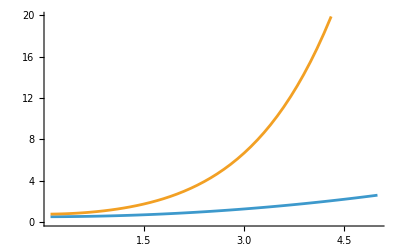

```mathematica
Plot[Evaluate[{Vxx+Δ^2/12,(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)/(2800 (12 Vxx+Δ^2))}/.{Vxx->0.5}],{Δ,0.1,5}]
```

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0] ;
bx=Integrate[θ*B2 p[θ]/.{x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0];//Simplify
bx2=Integrate[θ*B3 p[θ]/.{x^3->(x0+θ)^3+3*(x0+θ)*Vxx,x^2->(x0+θ)^2+Vxx,x->(x0+θ)},{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->Δ>0];//Simplify

bvec={b0,bx,bx2};
bvec//Simplify
```

{μ0,Δ^2/12,-(Vxx Δ^4)/(10 (12 Vxx+Δ^2))}

```mathematica
(* Solve G alpha=b *)
αopt=Simplify[Inverse[Gmat].bvec]

(* Write in terms of prior variance *)
αopt /. Δ^2->12*σ0^2//Simplify
```

{μ0,Δ^2/(12 Vxx+Δ^2),-(280 Vxx Δ^4)/(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)}

{μ0,σ0^2/(Vxx+σ0^2),-(280 Vxx Δ^4)/(201600 Vxx^4+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8+806400 Vxx^3 σ0^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,μ0-Δ/2,μ0+Δ/2},Assumptions->σ0>0]//Simplify

MSL=λ-bvec.Inverse[Gmat].bvec//Simplify
```

Δ^2/12+μ0^2

(Vxx Δ^2 (16800 Vxx^3+4200 Vxx^2 Δ^2+140 Vxx Δ^4+Δ^6))/(201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)

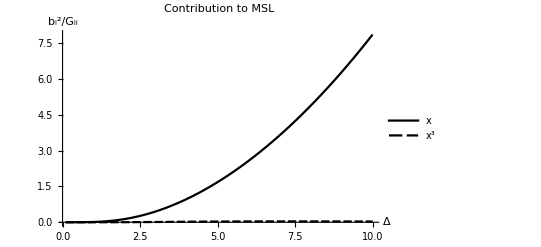

```mathematica
Plot[Evaluate[{((Δ^2/12)^2)/(Vxx+Δ^2/12),((Vxx Δ^4)/(10 (12 Vxx+Δ^2)))^2/((201600 Vxx^4+67200 Vxx^3 Δ^2+5880 Vxx^2 Δ^4+180 Vxx Δ^6+Δ^8)/(2800 (12 Vxx+Δ^2)))}/.{Vxx->0.5}],{Δ,0.1,10},AxesLabel->{Δ,Subscript[b, i]^2/Subscript[G, ii]},PlotLabel->"Contribution to MSL", PlotLegends->{x,x^3},PlotTheme->"Monochrome"]
```

## Showing that the posterior mean for uniform prior only contains odd powers of x

```mathematica
p[θ_]:=PDF[UniformDistribution[{μ0-Δ/2,μ0+Δ/2}],θ] (*Uniform prior *)

likelihood[θ_,x_,x0_]:=PDF[NormalDistribution[x0+θ,Vxx],x];(*Gaussian likelihood of x-homodyne measurements. This comes the p-marginal of the (Gaussian) Wigner function *)
```

```mathematica
evidence=Integrate[likelihood[θ,x,x0]*p[θ],{θ,-Infinity,Infinity},Assumptions->{σ0,Vxx,Δ} ∈ PositiveReals]
```

(Erf[(2 x-2 x0+Δ-2 μ0)/(2 √2 Vxx)]+Erf[(-2 x+2 x0+Δ+2 μ0)/(2 √2 Vxx)])/(2 Δ)

```mathematica
Integrate[evidence,{x,-Infinity,Infinity},Assumptions->{σ0,Vxx,Δ} ∈ PositiveReals] (*The normalisation of the posterior, i.e. the evidence, is already normalised*)
```

1

```mathematica
posterior[θ_,x_,x0_]:=(likelihood[θ,x,x0]*p[θ])/evidence (*The posterior from Bayes rule*)
```

The posterior mean is then

```mathematica
posteriorMeanUniformPrior=Integrate[θ*posterior[θ,x,x0],{θ,-Infinity,Infinity},Assumptions->{σ0,Vxx,Δ} ∈ PositiveReals] //Simplify
```

(-ⅇ^(-(4 x^2+4 x0^2+Δ^2+8 x0 μ0+4 μ0^2-8 x (x0+μ0))/(4 Vxx^2)) (ⅇ^((2 x-2 x0+Δ-2 μ0)^2/(8 Vxx^2))-ⅇ^((-2 x+2 x0+Δ+2 μ0)^2/(8 Vxx^2))) √(2/π) Vxx+((x-x0) (2 x-2 x0+Δ-2 μ0) Erf[(√((2 x-2 x0+Δ-2 μ0)^2))/(2 √2 Vxx)])/(√((2 x-2 x0+Δ-2 μ0)^2))-((x-x0) (2 x-2 x0-Δ-2 μ0) Erf[(√((-2 x+2 x0+Δ+2 μ0)^2))/(2 √2 Vxx)])/(√((-2 x+2 x0+Δ+2 μ0)^2)))/(Erf[(2 x-2 x0+Δ-2 μ0)/(2 √2 Vxx)]+Erf[(-2 x+2 x0+Δ+2 μ0)/(2 √2 Vxx)])

```mathematica
(* Note the symmetry around the point Subscript[x, 0] + θ *)
posterior[θ,x,x0]==posterior[θ,2(x0+θ)-x,x0]//Simplify

posterior[θ,x+(x0+θ),x0]==posterior[θ,-x+(x0+θ),x0]//Simplify
```

True

True

```mathematica
(* So the posterior mean expanded around Subscript[x, 0]+Subscript[μ, 0] only contains odd terms*)

Series[posteriorMeanUniformPrior/.x->x0+μ0+u,{u,0,5}] //.{Sqrt[a_^2]:>a}//Simplify
```

(Δ μ0)/(√(Δ^2))+(1-(ⅇ^(-Δ^2/(8 Vxx^2)) Δ)/(√(2 π) Vxx Erf[Δ/(2 √2 Vxx)])) u+(ⅇ^(-Δ^2/(4 Vxx^2)) Δ (-6 √(2/π) Vxx Δ+ⅇ^(Δ^2/(8 Vxx^2)) (12 Vxx^2-Δ^2) Erf[Δ/(2 √2 Vxx)]) u^3)/(24 √(2 π) Vxx^5 Erf[Δ/(2 √2 Vxx)]^2)-((ⅇ^(-(3 Δ^2)/(8 Vxx^2)) Δ (240 √2 Vxx^2 Δ^2-60 ⅇ^(Δ^2/(8 Vxx^2)) √π Vxx Δ (12 Vxx^2-Δ^2) Erf[Δ/(2 √2 Vxx)]+√2 ⅇ^(Δ^2/(4 Vxx^2)) π (240 Vxx^4-40 Vxx^2 Δ^2+Δ^4) Erf[Δ/(2 √2 Vxx)]^2)) u^5)/(3840 (π^(3/2) Vxx^9 Erf[Δ/(2 √2 Vxx)]^3))+O[u]^6

## Quadratic basis {1,Δx^2,Δp^2}

Basis is {1,Δx^2,Δp^2} where Δx^2=(x̂)^2-⟨x^2⟩_ρ_0

```mathematica
(*Means: <x>_(ρ(θ))=Subscript[x, 0]+theta, <p>_(ρ(θ))=Subscript[p, 0] and a diagonal covariance matrix V*)
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];(*Gaussian prior *)

(*First moments of rho0*)
avgx2=Integrate[(Vxx+(x0+θ)^2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
avgp2=Vpp+p0^2 ;

(*Second moments of rho0. For a Gaussian, <X^4> =3 σ^2+6 σ^2 μ^2 + μ^4*)
avgx4ρ0=Integrate[(3 Vxx^2+6 Vxx (x0+θ)^2+(x0+θ)^4) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify
avgp4ρ0=3 Vpp^2+6 Vpp p0^2+p0^4

(*Cross moment <x^2 p^2>_(ρ(θ))=(Subscript[V, xx]+(Subscript[x, 0]+θ)^2)(Subscript[V, pp]+Subscript[p, 0]^2)-1/2 (the -1/2 comes from the commutator[x,p]=i via Weyl ordering)*)

avgx2p2ρ0=Integrate[((Vxx+(x0+θ)^2)(Vpp+p0^2)-1/2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify


(*Gram matrix *)
Gmat=({{1, 0, 0}, {0, avgp4ρ0-avgx2^2, avgx2p2ρ0-avgx2*avgp2}, {0, avgx2p2ρ0-avgx2*avgp2, avgp4ρ0-avgp2^2}});
Gmat//MatrixForm
```

3 Vxx^2+(x0+μ0)^4+6 (x0+μ0)^2 σ0^2+3 σ0^4+6 Vxx ((x0+μ0)^2+σ0^2)

p0^4+6 p0^2 Vpp+3 Vpp^2

-1/2+(p0^2+Vpp) (Vxx+(x0+μ0)^2+σ0^2)

(1 | 0 | 0
0 | p0^4+6 p0^2 Vpp+3 Vpp^2-(Vxx+(x0+μ0)^2+σ0^2)^2 | -1/2
0 | -1/2 | p0^4+6 p0^2 Vpp+3 Vpp^2-(p0^2+Vpp)^2)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  
bx=Integrate[θ (Vxx+(x0+θ)^2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-avgx2*μ0//Simplify  
bp=Integrate[θ (Vpp+p0^2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-avgp2*μ0//Simplify  

bvec={b0,bx,bp};
bvec//Simplify
```

μ0

2 (x0+μ0) σ0^2

0

{μ0,2 (x0+μ0) σ0^2,0}

```mathematica
(* Solve G alpha=*)
αopt=Simplify[Inverse[Gmat].bvec]

(*To second order in prior width Subscript[σ, 0]*)
αSeries=Normal[Series[αopt,{σ0,0,2}]]//Simplify
```

{μ0,(4 Vpp (2 p0^2+Vpp) (x0+μ0) σ0^2)/(-1/4+2 Vpp (2 p0^2+Vpp) (p0^4+6 p0^2 Vpp+3 Vpp^2-(Vxx+(x0+μ0)^2+σ0^2)^2)),((x0+μ0) σ0^2)/(-1/4+2 Vpp (2 p0^2+Vpp) (p0^4+6 p0^2 Vpp+3 Vpp^2-(Vxx+(x0+μ0)^2+σ0^2)^2))}

{μ0,(4 Vpp (2 p0^2+Vpp) (x0+μ0) σ0^2)/(-1/4+2 Vpp (2 p0^2+Vpp) (p0^4+6 p0^2 Vpp+3 Vpp^2-(Vxx+(x0+μ0)^2)^2)),((x0+μ0) σ0^2)/(-1/4+2 Vpp (2 p0^2+Vpp) (p0^4+6 p0^2 Vpp+3 Vpp^2-(Vxx+(x0+μ0)^2)^2))}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

λ-bvec.Inverse[Gmat].bvec//Simplify
```

μ0^2+σ0^2

σ0^2-(8 Vpp (2 p0^2+Vpp) (x0+μ0)^2 σ0^4)/(-1/4+2 Vpp (2 p0^2+Vpp) (p0^4+6 p0^2 Vpp+3 Vpp^2-(Vxx+(x0+μ0)^2+σ0^2)^2))

## Symmetric logarithmic derivative (SLD) and Quantum Fisher Information (QFI)

We want to obtain the symmetric logarithmic derivative. For a Gaussian state, it is a quadratic form of position and momentum (x and p) 

ℒ=∑_ij L_ij 1/2{R_i-d_i,R_j-d_j}_++∑_i b_i(R_i-d_i)-1/2 tr{L Γ},

here, d_i=⟨R_i⟩=tr{R_i ρ}, R⃗=(x,p), Γ=2σ and σ_ij=1/2⟨{R_i,R_j}_+⟩ are the elements of the (symmetrized) covariance matrix. See Monras (2013) https://arxiv.org/pdf/1303.3682.

Here, Ω=(0 | -1
1 | 0) is the symplectic matrix. 

The coefficients are given by

L=𝒟_Γ^-1(∂Γ)
b⃗=2 Γ^-1∂d⃗.

For displacements encoded in the mean of the Wigner function, ∂Γ=0 and so the SLD is linear in the quadratures.

The linear term b⃗=2 Γ^-1∂d⃗ is

```mathematica
covDisplacement=({{Vxx, 0}, {0, Vpp}}); (* Covariance matrix*)

Γ=2*covDisplacement; (* Monras uses a different notation with a factor of 2 *)

d[θ_]:={x0+θ,p0}; (* Mean of Wigner function*)

dd=D[d[θ],θ];
```

```mathematica
b=2*Inverse[Γ].dd//FullSimplify
```

{1/Vxx,0}

The constant term is -1/2tr{L Γ}=0 since the quadratic L =0.

The QFI is then Tr(ρ(θ)ℒ^2)

```mathematica
Clear[x,p]
```

```mathematica
Expand[(b.({x,p}-d[θ]))^2]/.{x^2->Vxx+(x0+θ)^2,x->x0+θ}//Simplify
```

1/Vxx

```mathematica
Series[(Vxx σ0^2)/(Vxx+σ0^2),{σ0,0,4}] (* Compare to MSL for small Subscript[σ, 0]*)
```

σ0^2-σ0^4/Vxx+O[σ0]^5